## Introduction

Want to study the stability of the static sync state for swarmalators on a ring here

## Single δ: θ_i=x_i=0

### Form Jacobian

```mathematica
n=3;
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
J=Table[Join[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}]],{l,1,Length[eqnsdot]}]
```

{{1/3 j (-Cos[x_1-x_2] Cos[θ_1-θ_2]-Cos[x_1-x_3] Cos[θ_1-θ_3]),1/3 j Cos[x_1-x_2] Cos[θ_1-θ_2],1/3 j Cos[x_1-x_3] Cos[θ_1-θ_3],1/3 j (Sin[x_1-x_2] Sin[θ_1-θ_2]+Sin[x_1-x_3] Sin[θ_1-θ_3]),-1/3 j Sin[x_1-x_2] Sin[θ_1-θ_2],-1/3 j Sin[x_1-x_3] Sin[θ_1-θ_3]},{1/3 j Cos[x_1-x_2] Cos[θ_1-θ_2],1/3 j (-Cos[x_1-x_2] Cos[θ_1-θ_2]-Cos[x_2-x_3] Cos[θ_2-θ_3]),1/3 j Cos[x_2-x_3] Cos[θ_2-θ_3],-1/3 j Sin[x_1-x_2] Sin[θ_1-θ_2],1/3 j (Sin[x_1-x_2] Sin[θ_1-θ_2]+Sin[x_2-x_3] Sin[θ_2-θ_3]),-1/3 j Sin[x_2-x_3] Sin[θ_2-θ_3]},{1/3 j Cos[x_1-x_3] Cos[θ_1-θ_3],1/3 j Cos[x_2-x_3] Cos[θ_2-θ_3],1/3 j (-Cos[x_1-x_3] Cos[θ_1-θ_3]-Cos[x_2-x_3] Cos[θ_2-θ_3]),-1/3 j Sin[x_1-x_3] Sin[θ_1-θ_3],-1/3 j Sin[x_2-x_3] Sin[θ_2-θ_3],1/3 j (Sin[x_1-x_3] Sin[θ_1-θ_3]+Sin[x_2-x_3] Sin[θ_2-θ_3])},{-1/3 k (Sin[x_1-x_2] Sin[θ_1-θ_2]+Sin[x_1-x_3] Sin[θ_1-θ_3]),1/3 k Sin[x_1-x_2] Sin[θ_1-θ_2],1/3 k Sin[x_1-x_3] Sin[θ_1-θ_3],-F Cos[θ_1]-1/3 k (-Cos[x_1-x_2] Cos[θ_1-θ_2]-Cos[x_1-x_3] Cos[θ_1-θ_3]),-1/3 k Cos[x_1-x_2] Cos[θ_1-θ_2],-1/3 k Cos[x_1-x_3] Cos[θ_1-θ_3]},{1/3 k Sin[x_1-x_2] Sin[θ_1-θ_2],-1/3 k (Sin[x_1-x_2] Sin[θ_1-θ_2]+Sin[x_2-x_3] Sin[θ_2-θ_3]),1/3 k Sin[x_2-x_3] Sin[θ_2-θ_3],-1/3 k Cos[x_1-x_2] Cos[θ_1-θ_2],-F Cos[θ_2]-1/3 k (-Cos[x_1-x_2] Cos[θ_1-θ_2]-Cos[x_2-x_3] Cos[θ_2-θ_3]),-1/3 k Cos[x_2-x_3] Cos[θ_2-θ_3]},{1/3 k Sin[x_1-x_3] Sin[θ_1-θ_3],1/3 k Sin[x_2-x_3] Sin[θ_2-θ_3],-1/3 k (Sin[x_1-x_3] Sin[θ_1-θ_3]+Sin[x_2-x_3] Sin[θ_2-θ_3]),-1/3 k Cos[x_1-x_3] Cos[θ_1-θ_3],-1/3 k Cos[x_2-x_3] Cos[θ_2-θ_3],-1/3 k (-Cos[x_1-x_3] Cos[θ_1-θ_3]-Cos[x_2-x_3] Cos[θ_2-θ_3])-F Cos[θ_3]}}

```mathematica
J/.subs//TableForm
```

-(6 j)/7 | j/7 | j/7 | j/7 | j/7 | j/7 | j/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/7 | -(6 j)/7 | j/7 | j/7 | j/7 | j/7 | j/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/7 | j/7 | -(6 j)/7 | j/7 | j/7 | j/7 | j/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/7 | j/7 | j/7 | -(6 j)/7 | j/7 | j/7 | j/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/7 | j/7 | j/7 | j/7 | -(6 j)/7 | j/7 | j/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/7 | j/7 | j/7 | j/7 | j/7 | -(6 j)/7 | j/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/7 | j/7 | j/7 | j/7 | j/7 | j/7 | -(6 j)/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (6 k)/7-F √(1-Δ^2/F^2) | -k/7 | -k/7 | -k/7 | -k/7 | -k/7 | -k/7
0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/7 | (6 k)/7-F √(1-Δ^2/F^2) | -k/7 | -k/7 | -k/7 | -k/7 | -k/7
0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/7 | -k/7 | (6 k)/7-F √(1-Δ^2/F^2) | -k/7 | -k/7 | -k/7 | -k/7
0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/7 | -k/7 | -k/7 | (6 k)/7-F √(1-Δ^2/F^2) | -k/7 | -k/7 | -k/7
0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/7 | -k/7 | -k/7 | -k/7 | (6 k)/7-F √(1-Δ^2/F^2) | -k/7 | -k/7
0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/7 | -k/7 | -k/7 | -k/7 | -k/7 | (6 k)/7-F √(1-Δ^2/F^2) | -k/7
0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/7 | -k/7 | -k/7 | -k/7 | -k/7 | -k/7 | (6 k)/7-F √(1-Δ^2/F^2)

### Analyze at fixed point x_i=0, θ_i=0

#### Just J

```mathematica
n=10;
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
J=Table[Join[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}]],{l,1,Length[eqnsdot]}];
subs=Join[{Table[Subscript[x, i]->0,{i,1,n}],Table[Subscript[θ, i]->ArcSin[Δ/F],{i,1,n}]}]//Flatten;
TableForm[J/.subs]
```

-(9 j)/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/10 | -(9 j)/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/10 | j/10 | -(9 j)/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/10 | j/10 | j/10 | -(9 j)/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/10 | j/10 | j/10 | j/10 | -(9 j)/10 | j/10 | j/10 | j/10 | j/10 | j/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/10 | j/10 | j/10 | j/10 | j/10 | -(9 j)/10 | j/10 | j/10 | j/10 | j/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | -(9 j)/10 | j/10 | j/10 | j/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | -(9 j)/10 | j/10 | j/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | -(9 j)/10 | j/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | j/10 | -(9 j)/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (9 k)/10-F √(1-Δ^2/F^2) | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/10 | (9 k)/10-F √(1-Δ^2/F^2) | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/10 | -k/10 | (9 k)/10-F √(1-Δ^2/F^2) | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/10 | -k/10 | -k/10 | (9 k)/10-F √(1-Δ^2/F^2) | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/10 | -k/10 | -k/10 | -k/10 | (9 k)/10-F √(1-Δ^2/F^2) | -k/10 | -k/10 | -k/10 | -k/10 | -k/10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | (9 k)/10-F √(1-Δ^2/F^2) | -k/10 | -k/10 | -k/10 | -k/10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | (9 k)/10-F √(1-Δ^2/F^2) | -k/10 | -k/10 | -k/10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | (9 k)/10-F √(1-Δ^2/F^2) | -k/10 | -k/10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | (9 k)/10-F √(1-Δ^2/F^2) | -k/10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | -k/10 | (9 k)/10-F √(1-Δ^2/F^2)

There’s a clean block structure here. Excellent. Should be findble analytically then.

#### Find λ

```mathematica
n=3;
xdot=Table[j/n Sum[Sin[Subscript[x, j]-Subscript[x, i]]Cos[Subscript[θ, j]-Subscript[θ, i]],{j,1,n}],{i,1,n}];
thetadot=Table[Δ-F Sin[Subscript[θ, i]]-k/n Sum[Sin[Subscript[θ, j]-Subscript[θ, i]]Cos[Subscript[x, j]-Subscript[x, i]],{j,1,n}],{i,1,n}];
eqnsdot=Join[{xdot,thetadot}]//Flatten;
J=Table[Join[Table[D[eqnsdot[[l]], Subscript[x, i]],{i,1,n}],Table[D[eqnsdot[[l]], Subscript[θ, i]],{i,1,n}]],{l,1,Length[eqnsdot]}];
subs=Join[{Table[Subscript[x, i]->0,{i,1,n}],Table[Subscript[θ, i]->ArcSin[Δ/F],{i,1,n}]}]//Flatten;
λ=Eigenvalues[J/.subs/.Δ->1];
TableForm[λ]
```

0
-j
-j
1/3 Root[-27 F √((-1+F^2)/F^2)+27 F^3 √((-1+F^2)/F^2)+54 k-54 F^2 k+27 F √((-1+F^2)/F^2) k^2+(-27+27 F^2-36 F √((-1+F^2)/F^2) k+9 k^2) #1+(9 F √((-1+F^2)/F^2)-6 k) #1^2+#1^3&,1]
1/3 Root[-27 F √((-1+F^2)/F^2)+27 F^3 √((-1+F^2)/F^2)+54 k-54 F^2 k+27 F √((-1+F^2)/F^2) k^2+(-27+27 F^2-36 F √((-1+F^2)/F^2) k+9 k^2) #1+(9 F √((-1+F^2)/F^2)-6 k) #1^2+#1^3&,2]
1/3 Root[-27 F √((-1+F^2)/F^2)+27 F^3 √((-1+F^2)/F^2)+54 k-54 F^2 k+27 F √((-1+F^2)/F^2) k^2+(-27+27 F^2-36 F √((-1+F^2)/F^2) k+9 k^2) #1+(9 F √((-1+F^2)/F^2)-6 k) #1^2+#1^3&,3]

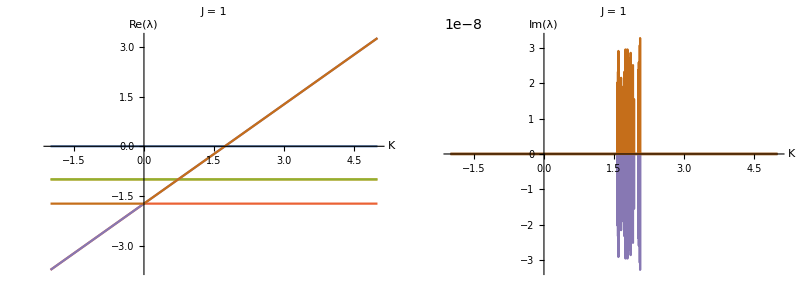

```mathematica
Clear[k1]
{j1,F1}={1,2};
p1=Plot[Re[λ]/.{j->j1,k->k1,F->F1}//Evaluate,{k1,-2,5},AxesOrigin->{0,0},AxesLabel->{"K","Re(λ)"},PlotLabel->"J = "<>ToString[j1],ImageSize->Medium];
p2=Plot[Im[λ]/.{j->j1,k->k1,F->F1}//Evaluate,{k1,-2,5},AxesOrigin->{0,0},AxesLabel->{"K","Im(λ)"},PlotLabel->"J = "<>ToString[j1],ImageSize->Medium];
Grid[{{p1,p2}}]
```

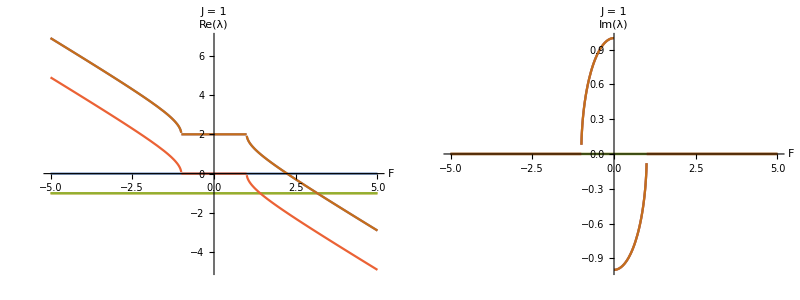

```mathematica
Clear[F1]
{j1,k1}={1,2};
p1=Plot[Re[λ]/.{j->j1,k->k1,F->F1}//Evaluate,{F1,-5,5},AxesOrigin->{0,0},AxesLabel->{"F","Re(λ)"},PlotLabel->"J = "<>ToString[j1],ImageSize->Medium];
p2=Plot[Im[λ]/.{j->j1,k->k1,F->F1}//Evaluate,{F1,-5,5},AxesOrigin->{0,0},AxesLabel->{"F","Im(λ)"},PlotLabel->"J = "<>ToString[j1],ImageSize->Medium];
Grid[{{p1,p2}}]
```

## Circulant matrix

```mathematica
n=10;
temp1=(n-1)/n k-F √(1-Δ^2/F^2);
temp2=Table[-k/n,{i,1,n-1}];
c1=Join[{temp1,temp2}]//Flatten//FullSimplify;
lams=Table[
{ω}={Exp[ (2 π ⅈ)/n]};
Total[Table[c1[[i+1]] ω^(i j),{i,0,n-1}]]//FullSimplify//Apart,
{j,0,n-1}
];
TableForm[lams]
```

-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)
k-F √((F^2-Δ^2)/F^2)

```mathematica
Solve[(k-F √((F^2-Δ^2)/F^2)/.{Δ->1,k->2})==0,F]//N
```

{{F→2.23607}}

```mathematica
{{k->F √((-1+F^2)/F^2)}}
```

```mathematica
p1=ContourPlot[{(k-F √((F^2-Δ^2)/F^2)/.Δ->1)==0,(-F √((F^2-Δ^2)/F^2)/.Δ->-0.5)==0}//Evaluate,{k,-2,2},{F,-2,2},FrameLabel->{Style["K",15,Italic],Style["F",15,Italic]},PlotStyle->Black,
Epilog->{
Text["Pinned state",{0.5,1.5}],
Text["Pinned state",{-0.5,-1.5}],
Blue,Line[{{0,1},{0,2}}]
}
]
```

```mathematica
Solve[k-F √((F^2-Δ^2)/F^2)==0,F]
```

{{F→-√(k^2+Δ^2)},{F→√(k^2+Δ^2)}}

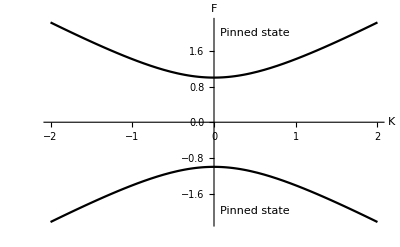

```mathematica
p1=Plot[{√(k^2+Δ^2),-√(k^2+Δ^2)}/.Δ->1,{k,-2,2},AxesLabel->{Style["K",15,Italic],Style["F",15,Italic]},PlotStyle->Black,
Epilog->{
Text["Pinned state",{0.5,2}],
Text["Pinned state",{0.5,-2}]
}
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["bif-diagram-F-k.png",p1];
```